### Impotering af billeder og resize

```mathematica
filepath:=SystemDialogInput["FileOpen",WindowTitle->"Select a Image to Open"]
userimage=ImageResize[Import[filepath],500];
```

### påføre imageefect “Stippling”

```mathematica
userimagegray = ColorConvert[ColorNegate[userimage],"Grayscale"];
userimagepoint=ImageEffect[userimagegray,{"Stippling",100}];
```

```mathematica
poss=PixelValuePositions[userimagepoint,1];
route=FindShortestTour[poss][[2]];
possroute=Append[poss[[route]],poss[[route]][[2]]];

possroute
```

{{138,351},{136,347},{139,347},{140,347},{140,346},{139,345},{138,345},{138,344},{137,344},{136,343},{137,342},{137,341},{136,342},{135,343},{135,342},{136,341},{136,340},{135,340},{136,339},{135,339},{134,340},{135,341},{134,342},{133,342},{133,343},{132,342},{132,343},{131,342},{130,343},{130,344},{129,344},{128,346},{127,345},{127,344},{128,344},{129,343},{130,342},46424,{135,337},{134,337},{135,336},{135,335},{134,335},{133,335},{132,336},{133,336},{134,336},{133,337},{133,338},{134,339},{134,338},{135,338},{136,337},{137,337},{137,338},{137,339},{137,340},{138,341},{138,342},{138,343},{139,343},{140,343},{140,342},{140,341},{141,342},{142,342},{141,343},{142,344},{143,346},{143,348},{141,350},{139,351},{138,351},{136,347}}
 |  |  |  |

### Scaling and Transforming

```mathematica
scale=100;
max=x/.Solve[Max[possroute]/x==scale,x][[1]];
For[i=1,i≤  Length[possroute],i++,
possroute[[i]]={(possroute[[i]][[1]])/max//N,(possroute[[i]][[2]])/max//N};
]
For[i=1,i≤  Length[possroute],i++,
possroute[[i]]={possroute[[i]][[1]]-((ImageDimensions[userimage][[1]])/max)/2,possroute[[i]][[2]]-((ImageDimensions[userimage][[2]])/max)/2}
]
```

### Viser et previw af ruten

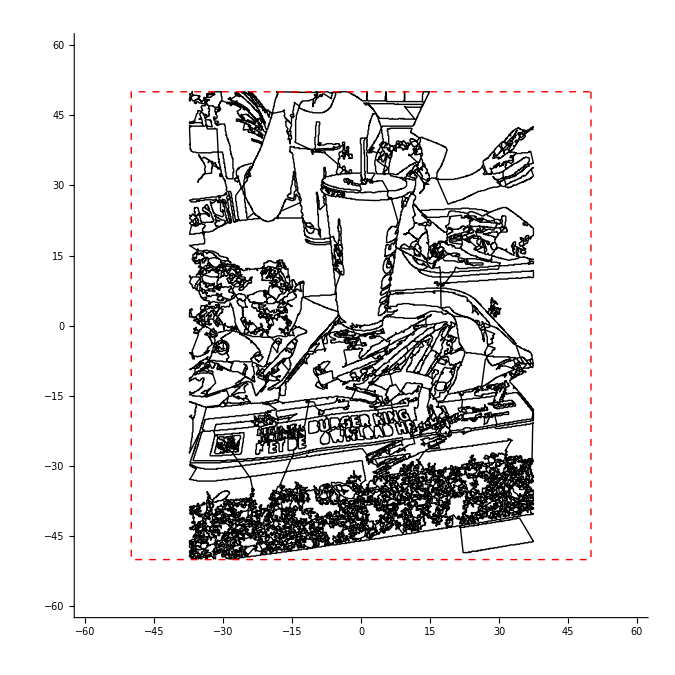

```mathematica
box={{50,50},{50,-50},{-50,-50},{-50,50},{50,50}};
Show[Graphics[Line[possroute],Axes->True,PlotRange->{{-60,60},{-60,60}}],
Graphics[{Dashed,Red,Line[box]},Axes->True,PlotRange->{{-60,60},{-60,60}}]]
```

### fsddsfdsfsdfsdfsdfsdfsdfsdfsdfsdf

```mathematica
travel:=Table[EuclideanDistance[possroute[[i]],possroute[[i+1]]],{i,1,Length[possroute]-1}]
maxlength=5;
trtotal=0;
isoroute={};
maxtravel=Sqrt[(1/max)^2+(1/max)^2];
For[i=1,i≤  Length[possroute]-1,i++,
AppendTo[isoroute,Flatten[{possroute[[i+1]],01,-0.5}]];
trtotal=trtotal+EuclideanDistance[possroute[[i]],possroute[[i+1]]];
If[trtotal≥maxlength,
AppendTo[isoroute,Insert[Insert[{0,0},98,3],-30,4]];trtotal=0;
AppendTo[isoroute,isoroute[[Length[isoroute]-1]]]
]
]
```

```mathematica
AppendTo[isoroute,{0,0,98,-35}]
```

{{-22.8,19.4,1,-0.5},{-22.2,19.4,1,-0.5},{-22.,19.4,1,-0.5},{-22.,19.2,1,-0.5},{-22.2,19.,1,-0.5},{-22.4,19.,1,-0.5},{-22.4,18.8,1,-0.5},{-22.6,18.8,1,-0.5},{-22.8,18.6,1,-0.5},{-22.6,18.4,1,-0.5},{-22.6,18.2,1,-0.5},46524,{-21.6,18.4,1,-0.5},{-21.8,18.6,1,-0.5},{-21.6,18.8,1,-0.5},{-21.4,19.2,1,-0.5},{-21.4,19.6,1,-0.5},{-21.8,20.,1,-0.5},{-22.2,20.2,1,-0.5},{-22.4,20.2,1,-0.5},{-22.8,19.4,1,-0.5},{0,0,98,-35}}
 |  |  |  |

### indsætter codinater som gcode i en fil og expoter

```mathematica
file=CreateFile[];
Table[
If[ToString[isoroute[[i]][[3]]]=="98",
WriteLine[file,
"N"<>ToString[i]<>
" G"<>ToString[isoroute[[i]][[3]]]<>
" Z"<>ToString[isoroute[[i]][[4]]]
]
,
WriteLine[file,
"N"<>ToString[i]<>
" G"<>ToString[isoroute[[i]][[3]]]<>
" X"<>ToString[isoroute[[i]][[1]]]<>
" Y"<>ToString[isoroute[[i]][[2]]]<>
" Z"<>ToString[isoroute[[i]][[4]]]
]
]
,{i,1,Length[isoroute]}];

ex:=SystemDialogInput["FileSave",WindowTitle->"Select where to save"]
CopyFile[file,ex<>".nc"];
```